### ODE

```mathematica
DSolve[{y'[x]==y[x]},y[x],x]
```

{{y[x]→ⅇ^x C[1]}}

```mathematica
y[x]/.DSolve[{y'[x]==y[x]},y[x],x]
```

{ⅇ^x C[1]}

#### With initial conditions

```mathematica
sol = DSolve[{y'[x]==y[x], y[0]==1}, y[x],x]
```

{{y[x]→ⅇ^x}}

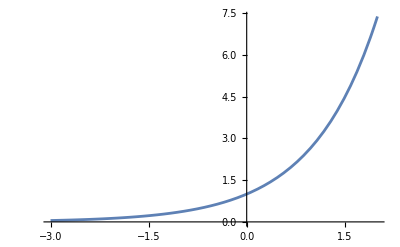

```mathematica
Plot[y[x]/.sol, {x, -3, 2}]
```

#### Solution as a pure function

```mathematica
eqn = {y'[x] == y[x]^2, y[0] == 1};
sol = DSolve[eqn, y ,x]
```

{{y→Function[{x},1/(1-x)]}}

```mathematica
eqn /.sol
```

{{True,True}}

### System of ODEs - constant coefficients

```mathematica
eqns={
(t^2+1)*x'[t]==-t*x[t]+y[t]-Sign[t],
(t^2+1)*y'[t]==-x[t]-t*y[t]+t*UnitStep[t],
x[0]==-1/2,y[0]==2
}
```

{(1+t^2) x'[t]==-Sign[t]-t x[t]+y[t],(1+t^2) y'[t]==t UnitStep[t]-x[t]-t y[t],x[0]==-1/2,y[0]==2}

```mathematica
sol=DSolve[eqns,{x,y},t]
```

{{x→Function[{t},(-1+4 t+2 (Piecewise[{{ArcTan[t], t≤0}, {-t, True}}])+2 t (Piecewise[{{1/2 Log[1+t^2], t≤0}, {0, True}}]))/(2 (1+t^2))],y→Function[{t},(4+t-2 t (Piecewise[{{ArcTan[t], t≤0}, {-t, True}}])+2 (Piecewise[{{1/2 Log[1+t^2], t≤0}, {0, True}}]))/(2 (1+t^2))]}}

```mathematica
eqns /.sol/. {t-> RandomReal[]}
```

{{True,True,True,True}}

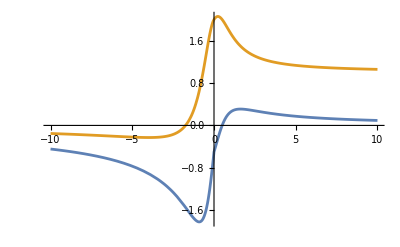

```mathematica
Plot[{x[t]/.sol,y[t]/.sol}, {t, -10, 10}]
```

### PDEs

```mathematica
eqn = x^2 * D[u[x,y],x] + y^2 *D[u[x,y],y] - (x+y)*u[x,y];
sol = DSolve[eqn== 0, u, {x,y}]
```

{{u→Function[{x,y},x y C[1][1/x-1/y]]}}

```mathematica
fn = u[x,y]/.sol[[1]]/. { [t_] -> Sin[t^2] + (t/10)}
```

x y C[1][1/x-1/y]

#### DSolve Tutorial - Working with DSolve

https://reference.wolfram.com/language/tutorial/DSolveWorkingWithDSolve.html